## BRDF Definitions

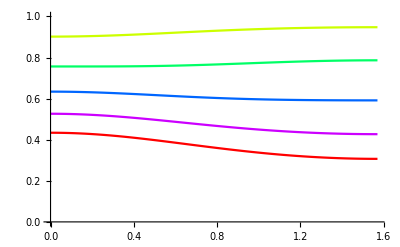

```mathematica
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=(2*Cos[θ])/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
lambda[θ_,α_]:=1/2(√(1+(α*Tan[θ])^2)-1)
smith2[θl_,θv_,α_]:=smith[θv,α] * smith[θl,α]
smith2[θl_,θv_,α_]:=(4*Cos[θl]*Cos[θv])/(2*Cos[θl]*√(Cos[θv]^2+α*Sin[θv]^2)+2*Cos[θv]*√(Cos[θl]^2+α*Sin[θl]^2))
smith2[θl_,θv_,α_]:=1/(1+lambda[θl,α]+lambda[θv,α])
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
BRDFggx[θo_,θi_,ϕi_,α_]:= (smith2[θo,θi,α]*ggx[change[θo,θi,ϕi],α])/(4*Cos[θo]*Cos[θi])

(*Eo[θo_,α_]:=smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]*)
Eo[θo_,α_]:=NIntegrate[BRDFggx[θo,θi,ϕi,α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
Show[Table[Plot[Eo[Cos[θ],α],{θ,0,π/2},PlotRange->{0,1},PlotStyle->Hue[α]],{α,0.2, 1, 0.2}]]
```

1/(1+lambda+lamda)

smith*smith

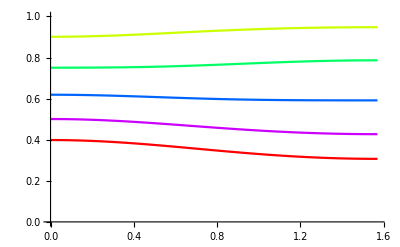

```mathematica
(*Manipulate[Plot[Eo[Cos[θ],α],{θ,0,π/2},PlotRange->{0,1}],{{α,1},0,1}]*)
```

Export (warning! SUPER LONG!)

```mathematica
countX = 128;
countY=128;
buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=Max[0.01,y];
{x,y,N[Eo[θo,α]]}
];
```

```mathematica
resultEo= Table[buildTable[i],{i,0,countX*countY-1}];
Export["MSBRDF_GGX_E128x128_G2.csv",resultEo,"CSV"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

## Tables Loading

Here, we want to make sure the irradiance tables computed by our MSBRDF notebook actually correspond to the magnitude values computed by the LTC fitter.
The temporary binary LTC file format I used contains 1 byte indicating whether the LTC is computed or not, then the 4 matrix elements m11, m22, m13 and m31 (double). Followed by the magnitude and fresnel integrated values (double). Followed by 3 vec3 values indicating the principal orientation of the M matrix (float). Finally followed by the error between the LTC and the actual BRDF (double).

```mathematica
(*LoadLTC=Function[{filename},
temp=BinaryReadList[filename,{ 
"Byte"
, "Real64", "Real64", "Real64", "Real64", "Real64", "Real64"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real64"}];(* Size of a single element = 1 + 7*8 + 9*4 = 93 *)
l=Length[temp];
s=N[Sqrt[l]];
N[l]
];*)

LoadLTC=Function[{filename},
(* Format contains Width and height as UINT32, followed by LTC elements *)
s=OpenRead[filename,BinaryFormat->True];
w=BinaryRead[s,"Integer32"];
h=BinaryRead[s,"Integer32"];

(* LTC elements are each a byte followed by the 6 double values + 3*3 floats describing a transform + a double representing the error between the BRDF and the LTC approximation *)
(* The table contains H rows where a row represents cos(θ)=1-y/H, y is the row index and θ is the view/light angle in [0,π/2] *)
(* The table contains W columns where a column represents α=(x/W)^2, x is the column index and α is the surface roughness in [0,1] *)
temp=Table[BinaryRead[s,{ 
"Byte"
, "Real64", "Real64", "Real64", "Real64", "Real64", "Real64"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real32", "Real32", "Real32"
, "Real64"}],{i,1,w*h}];
(*temp=Table[ Table[x + y * 10,{i,1,6}],{x,1,w},{y,1,h}];*)
Close[s];
l=Length[temp];
temp
];
ltc=LoadLTC["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables\\GGX.ltc"];
```

```mathematica
(*mags=Table[ltc[[x]][[y]][[6]],{x,1,64},{y,1,64}];
ListPlot3D[mags,AxesLabel->{"X","Y","Z"}]*)
```

```mathematica
mags=Table[{ 1-(Quotient[i,64]/63)^2,(Mod[i,64]/63)^2, ltc[[1+i]][[6]]},{i,0,64*64-1}];
ListPlot3D[mags,AxesLabel->{"α","cos(θ)","Z"},PlotRange->{0.3,1}]
```

-Graphics3D-

### GGX

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 

countX=16; countY=16;
resultEo = Import["MSBRDF_GGX_E16x16_G2.csv","CSV"];

countX=128; countY=128;
resultEo = Import["MSBRDF_GGX_E128x128.csv","CSV"];

resultEavg=Import["MSBRDF_GGX_Eavg128.csv","CSV"];
fEo=ListInterpolation[Table[resultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}];
fEavg=ListInterpolation[Table[resultEavg[[i]][[2]],{i,1,countY}],{0,1}];
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"},PlotRange->{0.3,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
```

-Graphics3D-

```mathematica
Show[
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"},PlotRange->{0.3,1}]
, ListPlot3D[mags,PlotStyle->Red]
]
```

-Graphics3D-